```mathematica
<<MASSToolbox`Style`
<<MASSToolbox`
```

```mathematica
SetDirectory[NotebookDirectory[]];
glycolysis=Import["../../models/SB2/glycolysis.m.gz"];
ppp=Import["../../models/SB2/ppp.m.gz"];
salvage=Import["../../models/SB2/salvage.m.gz"];
```

```mathematica
combi=Union[glycolysis,ppp,salvage];
(*combi=addSinks[combi];*)
```

```mathematica
combi=deleteReactions[combi,{"EX_g6p_c"}];
```

```mathematica
combi["InitialConditions"]
```

{glu^c→1. Millimole Liter^-1,fdp^c→0.0146 Millimole Liter^-1,dhap^c→0.16 Millimole Liter^-1,pg13^c→0.000243 Millimole Liter^-1,pg3^c→0.0773 Millimole Liter^-1,pg2^c→0.0113 Millimole Liter^-1,pep^c→0.017 Millimole Liter^-1,pyr^c→0.060301 Millimole Liter^-1,lac^c→1.36 Millimole Liter^-1,nad^c→0.0589 Millimole Liter^-1,nadh^c→0.0301 Millimole Liter^-1,v_vhk→1.12 Millimole Hour^-1 Liter^-1,v_vpgi→1.12 Millimole Hour^-1 Liter^-1,v_vpfk→1.12 Millimole Hour^-1 Liter^-1,v_vtpi→1.12 Millimole Hour^-1 Liter^-1,v_vald→1.12 Millimole Hour^-1 Liter^-1,v_vgapdh→2.24 Millimole Hour^-1 Liter^-1,v_vpgk→2.24 Millimole Hour^-1 Liter^-1,v_vpglm→2.24 Millimole Hour^-1 Liter^-1,v_veno→2.24 Millimole Hour^-1 Liter^-1,v_vpk→2.24 Millimole Hour^-1 Liter^-1,v_vldh→2.016 Millimole Hour^-1 Liter^-1,v_vapk→0. Millimole Hour^-1 Liter^-1,v_vpyr→0.224 Millimole Hour^-1 Liter^-1,v_vlac→2.016 Millimole Hour^-1 Liter^-1,v_vatp→2.24 Millimole Hour^-1 Liter^-1,v_vnadh→0.224 Millimole Hour^-1 Liter^-1,v_vgluin→1.12 Millimole Hour^-1 Liter^-1,v_vampin→0.014 Millimole Hour^-1 Liter^-1,g6p^c→0.0486 Millimole Liter^-1,f6p^c→0.0198 Millimole Liter^-1,gap^c→0.00728 Millimole Liter^-1,gl6p^c→0.00175424 Millimole Liter^-1,go6p^c→0.0374753 Millimole Liter^-1,ru5p^c→0.00493679 Millimole Liter^-1,x5p^c→0.0147842 Millimole Liter^-1,s7p^c→0.023988 Millimole Liter^-1,e4p^c→0.00507507 Millimole Liter^-1,nadp^c→0.0002 Millimole Liter^-1,nadph^c→0.0658 Millimole Liter^-1,gsh^c→3.2 Millimole Liter^-1,gssg^c→0.12 Millimole Liter^-1,co2^c→1. Millimole Liter^-1,v_vg6pdh→0.21 Millimole Hour^-1 Liter^-1,v_vpglase→0.21 Millimole Hour^-1 Liter^-1,v_vgl6pdh→0.21 Millimole Hour^-1 Liter^-1,v_vr5pe→0.133333 Millimole Hour^-1 Liter^-1,v_vr5pi→0.0766667 Millimole Hour^-1 Liter^-1,v_vtki→0.0666667 Millimole Hour^-1 Liter^-1,v_vtkii→0.0666667 Millimole Hour^-1 Liter^-1,v_vtala→0.0666667 Millimole Hour^-1 Liter^-1,v_vgssgr→0.42 Millimole Hour^-1 Liter^-1,v_vgshr→0.42 Millimole Hour^-1 Liter^-1,v_vco2→0.21 Millimole Hour^-1 Liter^-1,v_EX_f6p_c→0.133333 Millimole Hour^-1 Liter^-1,v_EX_r5p_c→0.01 Millimole Hour^-1 Liter^-1,v_EX_h_c→0.84 Millimole Hour^-1 Liter^-1,v_EX_h2o_c→-0.21 Millimole Hour^-1 Liter^-1,v_EX_gap_c→0.0666667 Millimole Hour^-1 Liter^-1,r5p^c→0.00494 Millimole Liter^-1,ade^c→0.001 Millimole Liter^-1,ado^c→0.0012 Millimole Liter^-1,imp^c→0.01 Millimole Liter^-1,ino^c→0.001 Millimole Liter^-1,hyp^c→0.002 Millimole Liter^-1,r1p^c→0.06 Millimole Liter^-1,prpp^c→0.005 Millimole Liter^-1,amp^c→0.0867281 Millimole Liter^-1,adp^c→0.29 Millimole Liter^-1,atp^c→1.6 Millimole Liter^-1,phos^c→2.5 Millimole Liter^-1,h^c→0.0000630957 Millimole Liter^-1,h2o^c→1. Millimole Liter^-1,nh3^c→0.091 Millimole Liter^-1,v_vak→0.12 Millimole Hour^-1 Liter^-1,v_vampase→0.12 Millimole Hour^-1 Liter^-1,v_vampda→0.014 Millimole Hour^-1 Liter^-1,v_vimpase→0.014 Millimole Hour^-1 Liter^-1,v_vada→0.01 Millimole Hour^-1 Liter^-1,v_vpnpase→0.014 Millimole Hour^-1 Liter^-1,v_vprm→0.014 Millimole Hour^-1 Liter^-1,v_vatpgen→0.148 Millimole Hour^-1 Liter^-1,v_vprppsyn→0.014 Millimole Hour^-1 Liter^-1,v_vadprt→0.014 Millimole Hour^-1 Liter^-1,v_vado→-0.01 Millimole Hour^-1 Liter^-1,v_vade→-0.014 Millimole Hour^-1 Liter^-1,v_vino→0.01 Millimole Hour^-1 Liter^-1,v_vhyp→0.014 Millimole Hour^-1 Liter^-1,v_vamp→0. Millimole Hour^-1 Liter^-1,v_vh→0. Millimole Hour^-1 Liter^-1,v_vh2o→-0.024 Millimole Hour^-1 Liter^-1,v_vphos→0. Millimole Hour^-1 Liter^-1,v_vnh3→0.024 Millimole Hour^-1 Liter^-1}

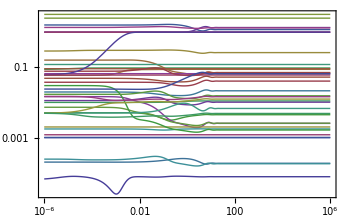

```mathematica
plotSimulation[simulate[combi,{t,0,1000000}][[1]]]
```

```mathematica
updateInitialConditions[combi,Flatten[findSteadyState[combi]]]
```

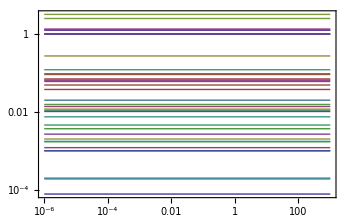

```mathematica
plotSimulation[simulate[combi,{t,0,1000}][[1]]]
```

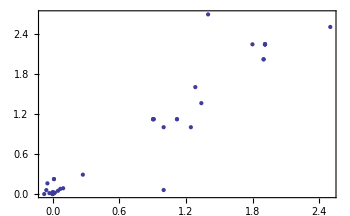

```mathematica
ListPlot[Thread[Tooltip[#[[All,2]],#[[All,1]]]]]&@stripUnits[scatterFromDicts[combi["InitialConditions"],glycolysis["InitialConditions"]]]
```

```mathematica
Thread[#->(#/.combi)]&[glycolysis["Fluxes"]]
Thread[#->(#/.combi)]&[ppp["Fluxes"]]
```

{v_vhk→1.12 Millimole Hour^-1,v_vpgi→0.910323 Millimole Hour^-1,v_vpfk→0.923564 Millimole Hour^-1,v_vtpi→0.923564 Millimole Hour^-1,v_vald→0.923564 Millimole Hour^-1,v_vgapdh→2.04356 Millimole Hour^-1,v_vpgk→2.04356 Millimole Hour^-1,v_vpglm→2.04356 Millimole Hour^-1,v_veno→2.04356 Millimole Hour^-1,v_vpk→2.04356 Millimole Hour^-1,v_vldh→2.02998 Millimole Hour^-1,v_vamp→0.014 Millimole Hour^-1,v_vapk→0. Millimole Hour^-1,v_vpyr→0.013584 Millimole Hour^-1,v_vlac→2.02998 Millimole Hour^-1,v_vatp→2.04356 Millimole Hour^-1,v_vnadh→0.013584 Millimole Hour^-1,v_vgluin→1.12 Millimole Hour^-1,v_vampin→0.014 Millimole Hour^-1,v_vh→1.45472 Millimole Hour^-1,v_vh2o→-0.104839 Millimole Hour^-1}

{v_vg6pdh→0.209677 Millimole Hour^-1,v_vpglase→0.209677 Millimole Hour^-1,v_vgl6pdh→0.209677 Millimole Hour^-1,v_vr5pe→0.133865 Millimole Hour^-1,v_vr5pi→0.0758128 Millimole Hour^-1,v_vtki→0.0669323 Millimole Hour^-1,v_vtkii→0.0669323 Millimole Hour^-1,v_vtala→0.0669323 Millimole Hour^-1,v_vgssgr→0.419355 Millimole Hour^-1,v_vgshr→0.419355 Millimole Hour^-1,v_vco2→0.209677 Millimole Hour^-1,v_EX_g6p_c→v_EX_g6p_c,v_EX_f6p_c→0.120623 Millimole Hour^-1,v_EX_r5p_c→0.00888056 Millimole Hour^-1,v_EX_h_c→1.45472 Millimole Hour^-1,v_EX_h2o_c→-0.104839 Millimole Hour^-1,v_EX_gap_c→-0.129504 Millimole Hour^-1}

```mathematica
combi["InitialConditions"]
```

{ade^c→0.000999925 Millimole Liter^-1,ado^c→0.00120036 Millimole Liter^-1,adp^c→0.272593 Millimole Liter^-1,amp^c→0.0954007 Millimole Liter^-1,atp^c→1.28517 Millimole Liter^-1,co2^c→1. Millimole Liter^-1,dhap^c→-0.0463741 Millimole Liter^-1,e4p^c→0.00367508 Millimole Liter^-1,f6p^c→0.0199173 Millimole Liter^-1,fdp^c→0.00266953 Millimole Liter^-1,g6p^c→0.0488289 Millimole Liter^-1,gap^c→-0.00415563 Millimole Liter^-1,gl6p^c→0.00173986 Millimole Liter^-1,glu^c→1.24497 Millimole Liter^-1,go6p^c→0.0375304 Millimole Liter^-1,gsh^c→3.18665 Millimole Liter^-1,gssg^c→0.120727 Millimole Liter^-1,h^c→0.0000770967 Millimole Liter^-1,h2o^c→0.999999 Millimole Liter^-1,hyp^c→0.002 Millimole Liter^-1,imp^c→0.011 Millimole Liter^-1,ino^c→0.00100001 Millimole Liter^-1,lac^c→1.33923 Millimole Liter^-1,nad^c→-0.0562381 Millimole Liter^-1,nadh^c→0.00170458 Millimole Liter^-1,nadp^c→0.000197355 Millimole Liter^-1,nadph^c→0.0648513 Millimole Liter^-1,nh3^c→0.0910002 Millimole Liter^-1,pep^c→0.0154525 Millimole Liter^-1,pg13^c→0.00018823 Millimole Liter^-1,pg2^c→0.0102012 Millimole Liter^-1,pg3^c→0.0697612 Millimole Liter^-1,phos^c→2.5 Millimole Liter^-1,prpp^c→0.00743568 Millimole Liter^-1,pyr^c→1.00002 Millimole Liter^-1,r1p^c→0.0602405 Millimole Liter^-1,r5p^c→0.0117461 Millimole Liter^-1,ru5p^c→0.00457808 Millimole Liter^-1,s7p^c→-0.0349544 Millimole Liter^-1,x5p^c→0.0137092 Millimole Liter^-1,v_EX_f6p_c→0.134123 Millimole Hour^-1,v_EX_gap_c→-0.0380552 Millimole Hour^-1,v_EX_h2o_c→-0.0751312 Millimole Hour^-1,v_EX_h_c→1.40009 Millimole Hour^-1,v_EX_r5p_c→0.00927156 Millimole Hour^-1,v_vada→0.010003 Millimole Hour^-1,v_vade→-0.0214772 Millimole Hour^-1,v_vado→0.0255804 Millimole Hour^-1,v_vadprt→0.0214772 Millimole Hour^-1,v_vak→0.0964162 Millimole Hour^-1,v_vald→0.905257 Millimole Hour^-1,v_vamp→-0.0281706 Millimole Hour^-1,v_vampase→0.132 Millimole Hour^-1,v_vampda→0.0154 Millimole Hour^-1,v_vampin→0.00133561 Millimole Hour^-1,v_vapk→1.38778×10^-12 Millimole Hour^-1,v_vatp→1.79924 Millimole Hour^-1,v_vatpgen→0.139116 Millimole Hour^-1,v_vco2→0.208234 Millimole Hour^-1,v_veno→1.91238 Millimole Hour^-1,v_vg6pdh→0.208234 Millimole Hour^-1,v_vgapdh→1.91238 Millimole Hour^-1,v_vgl6pdh→0.208234 Millimole Hour^-1,v_vgluin→1.12 Millimole Hour^-1,v_vgshr→0.416467 Millimole Hour^-1,v_vgssgr→0.416467 Millimole Hour^-1,v_vh→1.40009 Millimole Hour^-1,v_vh2o→-0.0751312 Millimole Hour^-1,v_vhk→1.12 Millimole Hour^-1,v_vhyp→0.0139363 Millimole Hour^-1,v_vimpase→0.0154 Millimole Hour^-1,v_vino→0.0114666 Millimole Hour^-1,v_vlac→1.89969 Millimole Hour^-1,v_vldh→1.89969 Millimole Hour^-1,v_vnadh→0.0126853 Millimole Hour^-1,v_vnh3→0.0254029 Millimole Hour^-1,v_vpfk→0.905257 Millimole Hour^-1,v_vpgi→0.911766 Millimole Hour^-1,v_vpgk→1.91238 Millimole Hour^-1,v_vpglase→0.208234 Millimole Hour^-1,v_vpglm→1.91238 Millimole Hour^-1,v_vphos→-0.0758333 Millimole Hour^-1,v_vpk→1.91238 Millimole Hour^-1,v_vpnpase→0.0139363 Millimole Hour^-1,v_vprm→0.0139363 Millimole Hour^-1,v_vprppsyn→0.0214772 Millimole Hour^-1,v_vpyr→0.0126853 Millimole Hour^-1,v_vr5pe→0.127614 Millimole Hour^-1,v_vr5pi→0.0806195 Millimole Hour^-1,v_vtala→0.0638071 Millimole Hour^-1,v_vtki→0.0638071 Millimole Hour^-1,v_vtkii→0.0638071 Millimole Hour^-1,v_vtpi→0.905257 Millimole Hour^-1}